# Building Blocks of Quantum Circuits

We will review the common procedure for a quantum algorithm: a state is prepared, some quantum operations are done, and then measurements. We will show how this is done within an object usually called quantum circuit. We will discuss each concept, eg quantum state, quantum operator, quantum basis and etc more.

## Key Concepts

Quantum State

Register State

Quantum Operator

Bloch Sphere

Computational Basis

## Quantum Operations

Let’s consider a generic quantum circuit as follows:

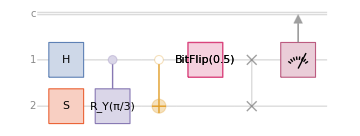

```mathematica
QuantumCircuitOperator[{"H","S"->2,"C"["RY"[π/3]]->{1,2},"C"["NOT"->2,{},{1}],"BitFlip","SWAP",{1}}]["Diagram"]
```

Let’s read this circuit step by step, although they are some details that you might not be familiar with:

Since no initial state is given, the two qubits are prepared in the register state 00

A Hadamard gate H acts on qubit 1.

An S gate acts on qubit 2.

A conditional rotation about Y by angle π/3 acts on both qubits: if qubit 1 is in state 1, apply the corresponding rotation on qubit 2; otherwise do nothing.

A conditional-0 NOT acts on both qubits: if qubit 1 is in state 0, apply an X (also called as NOT) to qubit 2; otherwise do nothing.

A bit-flip noise channel acts on qubit 1 with rate (probability) 50%.

A SWAP gate acts on both qubits.

Qubit 1 is measured in the computational basis.

In classical computation, we use rules to map input states to output states. Quantum operators serve a similar role: they are the rules that transform one quantum state into another. Unlike classical rules, however, they must obey specific constraints set by the formalism of quantum mechanics; for example, they are linear and usually unitary. In the language of quantum computing, you will often hear these operators described as “gates” or “gate operations.” This terminology is borrowed from classical computer engineering.

## Quantum States

In classical digital computing, states are represented by sequences of 1s and 0s. Each classical bit has two possible states, 0 or 1. A sequence of two bits has four possible states: “00,” “01,” “10,” or “11”. In general, a sequence of n classical bits has 2^n possible states.

Quantum states behave differently. When a quantum state is measured, the outcome is always a definite classical result. However, the act of measurement inevitably changes the state, this is known as state collapse. Unlike classical states, quantum states can exist in superpositions. Still, there are special quantum states called computational basis states that always yield the same classical result when measured. These states can be labeled directly by a classical bit string.

If quantum operators in a circuit diagram are the instructions for changing a state, what do we assume about the input state? By convention, most quantum circuit diagrams begin with the register state. This is the special basis state that always yields the classical result of all zeros when the qubits are measured.

The 1-qubit register state can be written as follows:

```mathematica
QuantumState["Register"]
```

QuantumState[…]

The Wolfram Quantum Framework returns a summary box for quantum objects because it is much more convenient in practice. Unless the system is very small, other notations—such as full Dirac expressions—are not especially useful for everyday work.

The traditional form of quantum state returns the conventional Dirac notation of the state:

```mathematica
QuantumState["Register"]//TraditionalForm
```

0

The above state can be written in different ways:

```mathematica
QuantumState["0"]
```

QuantumState[…]

Check they are the same:

```mathematica
QuantumState["Register"]==QuantumState["0"]
```

True

The 2-qubit register state can be written like this:

```mathematica
QuantumState["Register"[2]]//TraditionalForm
```

00

And so on:

```mathematica
TraditionalForm/@Table[QuantumState["Register"[n]],{n,3,6}]
```

{000,0000,00000,000000}

Throughout this course, we will follow big-endian (usual Dirac) convention, as opposed to little-endian (usual IBM) convention. In the big endian convention, a state such as 01 means qubit-1 is in the state 0 and qubit-2 is in the state 1.

A register state as 0^(⊗n) is a shorthand representation of a unit vector of length 2^n where the first element is one and all other elements are zero:

```mathematica
Table["n="<>ToString[n]->Normal@QuantumState[StringJoin@ConstantArray["0",n]]["StateVector"],{n,5}]//Column
```

n=1→{1,0}
n=2→{1,0,0,0}
n=3→{1,0,0,0,0,0,0,0}
n=4→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
n=5→{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

We will discuss quantum states in much more detail in the following chapters. For now, let’s focus on different visualizations of the state, without diving deeply into their full meaning.

## Bloch Sphere

Since qubits are not the same as classical bits, labeling them by classical bit sequences is insufficient to represent all possible qubit states. How then are quantum states represented?

Future lessons will discuss representing quantum states in more details. In fact, much of the formalism of quantum mechanics is an important application of linear algebra. However, there is a very useful graphical representation of 1-qubit states called the Bloch sphere.

The Bloch sphere is named after physicist Felix Bloch:

-Graphics-

In this approach, a quantum state is represented by a point in 3D space inside a sphere of radius 1 (the Bloch sphere). The point may lie on the surface, in which case we call it a pure state, or inside the sphere, in which case we call it a mixed state.

Compute the Bloch vector of 0:

```mathematica
QuantumState["0"]["BlochVector"]
```

{0,0,1}

The Bloch sphere representation of the qubit state 0 can be given as follows:

```mathematica
QuantumState["0"]["BlochPlot"]
```

-Graphics3D-

Compute the Bloch vector of 1:

```mathematica
QuantumState["1"]["BlochVector"]
```

{0,0,-1}

Notice that the qubit state 1 is on the opposite side of the sphere from 0.

```mathematica
QuantumState["1"]["BlochPlot"]
```

-Graphics3D-

The use of the sphere already suggests that the space of 1-qubit states is already quite a bit richer than only 0 or 1 as in classical bits. The states labeled +, -, L and R are other specific states the qubits can attain. However, the 0 and 1 states are usually called the computational basis states. In order to read out a result from the qubits that can be used in digital computation, you must measure the state of the qubit in the chosen computational basis.

Physically, there is some arbitrariness in how the states on the Bloch sphere are labeled. What matters is that the designer of a quantum computer chooses two easily measurable quantum states to serve as the logical values of a classical 0 and a classical 1. Quantum operations can then rotate or transform qubits into other states on the Bloch sphere; this ability is precisely what makes quantum computation more powerful than classical computation. In practice, however, the final step in a quantum circuit is always to measure the qubits in the chosen computational basis, so that the result can be expressed in classical bits.

When thinking about the state of a qubit, you can view it in several equivalent ways:

As a linear combination (a complex-valued 2-vector) in the computational basis.

As a 3-vector representing Cartesian coordinates of the Bloch vector {x,y,z}.

As the same point in spherical coordinates {r,ϕ,θ}.

For pure states, the Bloch vector lies on the unit sphere (r=1); for mixed states, it lies inside the sphere (0<=r<1). We will discuss the concept of pure and mixed states in more details later.

Generate different representations of a random state:

```mathematica
state=QuantumState["RandomPure"];
Grid[Transpose[{{"Dirac notation","State vector","Bloch vector","Bloch spherical coordinates","Bloch plot"},{TraditionalForm[state],state["AmplitudesList"],state["BlochVector"],state["BlochSphericalCoordinates"],state["BlochPlot"]}}],Frame->All,Alignment->Left]
```

Dirac notation | (-0.287995-0.39684 ⅈ)0+(0.653438+0.576711 ⅈ)1
State vector | {-0.287995-0.39684 ⅈ,0.653438+0.576711 ⅈ}
Bloch vector | {-0.834098,0.18644,-0.519153}
Bloch spherical coordinates | {1,2.11666,2.92168}
Bloch plot | -Graphics3D-

## Bra-Ket Notation

In the formalism of quantum mechanics, how to represent and write down the various concepts is an important question. For some common quantum operations, bra-ket notation is particularly useful. This is also sometimes called Dirac notation after P.A.M. Dirac.

-Graphics-

In general ket, …, is a shorthand representation for a vector, and bra, …, is the conjugate transpose of a ket. For example, we a qubit, we have:

```mathematica
Row[{ψ->MatrixForm[{α,β}],"  ",ψ->MatrixForm[{{SuperStar[α],SuperStar[β]}}]}]
```

ψ→(α
β)  ψ→(α^* | β^*)

From these definitions, a ket-bra as …… represents a matrix:

```mathematica
ClearAll[a,b,α,β]
Row[{"ψ"->MatrixForm[{a,b}],"  ","ϕ"->MatrixForm[{α,β}]," => ","ψϕ"->MatrixForm[KroneckerProduct[{a,b},{SuperStar[α],SuperStar[β]}]]}]
```

ψ→(a
b)  ϕ→(α
β) => ψϕ→(a α^* | a β^*
b α^* | b β^*)

Show the matrix form and also Dirac notation of NOT gate:

```mathematica
MatrixForm[QuantumOperator["NOT"]["Matrix"]]->TraditionalForm[QuantumOperator["NOT"]]
```

(0 | 1
1 | 0)→01+10

Show the elements in the Dirac notation of R_Y rotation with the angle π/3:

```mathematica
QuantumOperator["RY"[π/3]]["Table"]
```

| 0 | 1
0 | (√3)/2 | -1/2
1 | 1/2 | (√3)/2

Show the Dirac notation of controlled-Hadamard gate:

```mathematica
QuantumOperator["CH"]//TraditionalForm
```

0000+0101+1/(√2)1010+1/(√2)1011+1/(√2)1110-1/(√2)1111

In summary, the ket notation … represents a complex-valued vector, and the bra notation … can be understood as the conjugate transpose of a ket. When we have a composite state such as 00, it is shorthand for the tensor product 0⊗0; in a similar manner a notation like 01 means 0⊗1. We will discuss these details further in future chapters

## Effects of Operations on Qubits

Consider the following circuit:

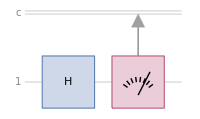

```mathematica
QuantumCircuitOperator[{"H",{1}}]["Diagram",ImageSize->200]
```

Let’s examine these operations in more detail. The gate labeled “H” is called a Hadamard gate, named after French mathematician Jacques Salomon Hadamard.

-Graphics-

What is the effect of this gate on a qubit in the register state?

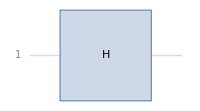
-Graphics- ⇒ -Graphics3D-

```mathematica
With[{circuit=QuantumCircuitOperator[{"H"->1}],size=200},
Row[{circuit["Diagram",ImageSize->{size,Automatic}],circuit[]["BlochPlot",ImageSize->size]},Style[" ⇒ ",Bold,20]]
]
```

```mathematica
TraditionalForm[QuantumState["0"]]->TraditionalForm[QuantumOperator["H"][]]
```

0→1/(√2)0+1/(√2)1

Notice that the qubit is no longer in either the 0 or 1 state. What will happen if you add a measurement in the computational basis?

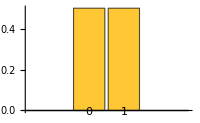
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"H"->1,"M"->1}],size=200},
Row[{circuit["Diagram",ImageSize->{size,Automatic}],circuit[]["ProbabilityPlot",ImageSize->size]},Style[" ⇒ ",Bold,20]]
]
```

After applying a Hadamard gate to the register state and measuring, you will have a 50-50 chance of obtaining the 0 or 1 outcomes. Notice the connection between the geometry of the Bloch sphere and these probabilities. After applying the Hadamard gate to the register state, the qubit’s state is “in the middle” of the 0/1 axis on the Bloch sphere. Measuring in the computational basis is like projection of that vector into Z-axis.

### A Quick Note on Measurement

You might wonder at what point probabilities enter the picture. Does the Hadamard gate introduce the need for probability or does the measurement? Before answering this question, what happens if the measurement is not done in the computational basis? What happens if a different measurement is performed with a special relationship to the Hadamard gate as shown below?

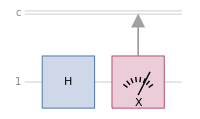
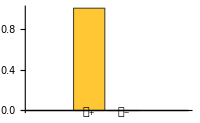
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"H"->1,"M"["X"]->1}],size=200},
Row[{circuit["Diagram",ImageSize->{size,Automatic}],circuit[]["ProbabilitiesPlot",ImageSize->size]},Style[" ⇒ ",Bold,20]]
]
```

Performing this new measurement (not the usual computational basis) gives the same result with 100% probability after applying the Hadamard gate. Thus, there are cases where measurement also does not lead to probabilistic results.

As shown in the Bloch plot, the qubit is in a definite quantum state after the Hadamard gate is applied:

```mathematica
With[{circuit=QuantumCircuitOperator[{"H"->1}],size=200},
Row[{circuit["Diagram",ImageSize->{size,Automatic}],circuit[]["BlochPlot",ImageSize->size]},Style[" ⇒ ",Bold,20]]
]
```

-Graphics- ⇒ -Graphics3D-

Measuring this particular qubit state along the +/- axis will always give the same result, as you saw from the plot of measurement probabilities.

Probability is only necessary when the quantum state before measurement is not in the same basis as the measurement being performed. If you want to know precise details about this feature of quantum mechanics, it is typically expressed in terms of eigenvalues and eigenvectors of matrices. You can learn about this mathematical formalism in a course on linear algebra.

## More Operations on Qubits

You have seen the effects of the Hadamard gate. What about the “NOT” operation? Unsurprisingly, applying the “NOT” operation to the register state changes 0 to 1 with 100% probability.

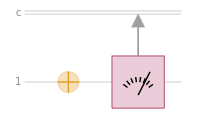
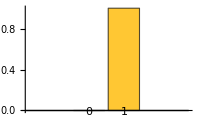
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"NOT"->1,"M"->1}],size=200},
Row[{circuit["Diagram",ImageSize->{size,Automatic}],circuit[]["ProbabilitiesPlot",ImageSize->size]},Style[" ⇒ ",Bold,20]]
]
```

Many important operations involve more than one qubit. One of the simplest is the “SWAP” operation. This just re-labels the qubits by swapping two of them:

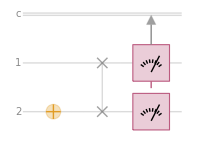
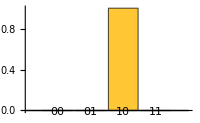
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"NOT"->2,"SWAP"->{1,2},"M"->{1,2}}]},
Row[{circuit["Diagram",ImageSize->{200,Automatic}],circuit[]["ProbabilitiesPlot",ImageSize->200]},Style[" ⇒ ",Bold,20]]
]
```

Notice how the results of this circuit are always the bit sequence “10”, even though the “NOT” operation was applied to the 2nd qubit. That’s because a “SWAP” is performed just after the “NOT” operation. Contrast this with the unswapped case:

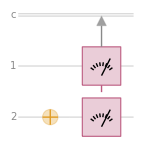
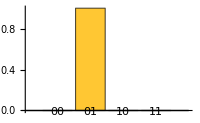
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"NOT"->2,"M"->{1,2}}]},
Row[{circuit["Diagram",ImageSize->{200,Automatic}],circuit[]["ProbabilitiesPlot",ImageSize->200]},Style[" ⇒ ",Bold,20]]
]
```

Controlled operations are another important category. One of the most common examples is the controlled not gate or “CNOT”:

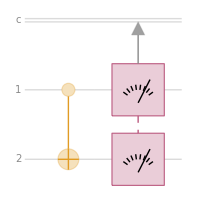
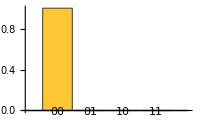
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"CNOT"->{1,2},"M"->{1,2}}]},
Row[{circuit["Diagram",ImageSize->{200,Automatic}],circuit[]["ProbabilitiesPlot",ImageSize->200]},Style[" ⇒ ",Bold,20]]
]
```

On this particular input, “CNOT” does not appear to do anything. That’s because a controlled gate can be thought of like an “if” statement. If the control qubit is a “1”, perform an operation on the target qubit. If the control qubit is a “0”, do nothing.

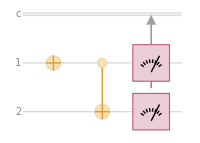
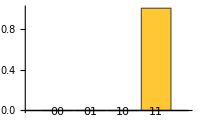
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"NOT","CNOT"->{1,2},"M"->{1,2}}]},
Row[{circuit["Diagram",ImageSize->{200,Automatic}],circuit[]["ProbabilitiesPlot",ImageSize->200]},Style[" ⇒ ",Bold,20]]
]
```

As you can see, changing the control qubit to a “1” now results in the NOT operation being applied to the target qubit.

In the context of qubits, the CNOT gate can be used to generate quantum states with very unique properties if the control qubit is in neither the “0” nor “1” state.

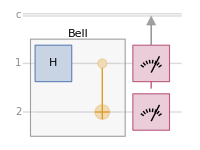
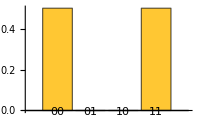
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"Bell","M"->{1,2}}]},
Row[{circuit["Diagram",ImageSize->{200,Automatic}],circuit[]["ProbabilitiesPlot",ImageSize->200]},Style[" ⇒ ",Bold,20]]
]
```

The circuit above no longer produces the same measurement outcome every time. Applying a Hadamard to the first qubit and then a CNOT (control on qubit 1, target on qubit 2) creates the Bell state 1/(√2)(00+11); so the outcomes are “00” with probability 50% and “11” with probability 50%. This is one of the famous Bell states, named after physicist John Bell. Notably, if you obtain 0 on qubit 1, qubit 2 is certainly 0, and similarly, if qubit 1 is 1, qubit 2 is certainly 1. We will discuss this perfect correlation (a consequence of entanglement) later.

-Graphics-

## Initialization

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]